## 1. Introduction to Wolfram Mathematica

### 1.1. Arithmetical Operations

Task: Find value of expression (0.134+0.05)/((18+1/6)-(1+11/14)-2/15 (2+6/7))

```mathematica
Clear[Answer]
Answer = (0.134+0.05)/((18+1/6)-(1+11/14)-2/15(2+6/7));
Print["Answer is ", Answer]
```

Answer is 0.0115

### 1.2. Evaluating expression containing solely elementary functions

Task: Find the value of expression

```mathematica
Clear[y,Answer]
y=1/3 Cos[1/Tan[3]]+1/5 (Sin[5 Sqrt[2]])^2/Cos[10 ⅇ^3];
Answer = N[y];
Print["Answer is ", Answer]
```

Answer is 0.350611

## 2. Algebraic Evaluation

### 2.1. Algebraic Manipulations

Task: Simplify expression

```mathematica
Clear[a,b,c,n,Result]
Result=Simplify[((2 a^2(b+c)^(2n)-1/2)/(a n^2-a^3-2 a^2-a))/((2a(b+c)^n-1)/(a^2 c-a(n c-c)))];
Print["Result is ", Result]
```

Result is -(c (1+2 a (b+c)^n))/(2 (1+a+n))

### 2.2. Finding values of algebraic expressions

Task: Calculate  for

```mathematica
Remove[a,b,Answer]
Expr = (Sqrt[a b]-(a b)/(a+Sqrt[a b]))/((Surd[a b,4]-Sqrt[b])/(a-b));
Answer = Simplify[Expr/.{a->8,b->2}];
Print["The answer is ", Answer]
```

The answer is 8 (2+√2)

### 2.3. Solving equations

Task: Solve equation  for

```mathematica
Clear[a,x]
Solve[1/a+1/(a+x)+1/(a+2 x)==0,x]
```

{{x→1/2 (-3 a-√3 a)},{x→1/2 (-3 a+√3 a)}}

## 3. Elements of Analytical Geometry

### 3.1. Operating with vectors

Task: For vectors  determine whether  and  are collinear. Find lengths of vectors  and  and angle between them. Draw vectors  and .

```mathematica
Clear[a,b,c1,c2]
a={-2,7,-1};
b={-3,5,2};
c1=2 a+3 b;
c2=3a+2b;
ratio=c1/c2;
Print["Ratio is ", ratio]
```

Ratio is {13/12,29/31,4}

We thus conclude that  and  are not collinear.

```mathematica
LengthOfA=Norm[a];
LengthOfB=Norm[b];
AngleAB=(N[VectorAngle[a,b]] 180)/π;
Print["Length of a is ", LengthOfA," and length of b is ", LengthOfB]
Print["Angle between a and b (in degrees) is ", AngleAB]
```

Length of a is Norm[a] and length of b is Norm[b]

Angle between a and b (in degrees) is (180 VectorAngle[a,b])/π

```mathematica
z={0,0,0}
Graphics3D[{Thickness[0.02],Arrowheads[0.1],Arrow[{z,a}],Arrow[{z,b}]},Axes->True,AxesLabel->{"x","y","z"}]
```

{0,0,0}

-Graphics3D-

### 3.2. Geometric calculations in Triangle

Task: Given triangle with vertices , find its sides, angles and area.

```mathematica
Unprotect[C];
A = {6,2,-3}; B = {6,3,-2}; C={7,3,-3};
ListPlot3D[{A,B,C},BoxRatios->Automatic,ColorFunction->"SouthwestColors"]
```

-Graphics3D-

```mathematica
AB=B-A; AC=C-A; BC=C-B;
LengthAB=Norm[AB];LengthAC=Norm[AC];LengthBC=Norm[BC];
angleA=VectorAngle[AB,AC];angleB=VectorAngle[-AB,BC]; angleC=VectorAngle[AC,BC];
Print["Lengths of sides AB, AC, and BC are ", LengthAB,", ",LengthAC,", ",LengthBC]
Print["Angles A, B, and C are ", angleA, ", ", angleB,", ", angleC]
```

Lengths of sides AB, AC, and BC are √2, √2, √2

Angles A, B, and C are π/3, π/3, π/3

```mathematica
S=1/2 Norm[Cross[AB,AC]];
Print["Area of triangle is ", S]
```

Area of triangle is (√3)/2

### 3.3. Calculations in Tetrahedron

Task. Given Tetrahedron with vertices , find its volume, height  from vertex  on side . Display this tetrahedron, height  and point .

```mathematica
Unprotect[A,B,C,D,E];
A={1,1,2};B={-1,1,3};C={2,-2,4};D={-1,0,-2};
AB=B-A;AC=C-A;AD=D-A;
V=1/6 Abs[Det[{AB,AC,AD}]];
n=-Cross[AB,AC];
S=1/2 Norm[n];
h=(3 V)/S;
E=D-n/(2S)h;
graph1=Graphics3D[{Thickness[0.01],Line[{A,B,C,A,D,B,C,D}]},AxesLabel->{"x","y","z"},Axes->True,BaseStyle->{Blue,Opacity[.7]}];
graph2=ListPointPlot3D[{E},PlotStyle->{Directive[PointSize[0.03],Red]}];
graph3=Graphics3D[{Thickness[0.01],{Dashed,Red,Line[{D,E}]}}];
graph4=Graphics3D[{Opacity[0.3],Gray,InfinitePlane[{A,B,C}]}];
Show[graph1,graph2,graph3,graph4]
```

-Graphics3D-

## 4. Matrix Calculations

### 4.1. Working with matrices

Task: Given matrices , find  where  is an identity matrix. Find inverse matrix . Find . Find sum and difference of . Find  and , find difference between these values. Solve matrix equation  with respect to .

```mathematica
A={{1,2,1},{0,2,0},{-1,1,1}};
B={{1,1,2},{0,2,1},{1,-1,0}};
M=2*A.A+3 A+5 IdentityMatrix[3];
Print["Matrix polynomial equals ",M//MatrixForm]
```

Matrix polynomial equals (8 | 20 | 7
0 | 19 | 0
-7 | 5 | 8)

```mathematica
InverseA=Inverse[A];
Print["Inverse of matrix A is ", InverseA//MatrixForm]
```

Inverse of matrix A is (1/2 | -1/4 | -1/2
0 | 1/2 | 0
1/2 | -3/4 | 1/2)

```mathematica
DetA=Det[A];
Print["det(A) = ", DetA]
```

det(A) = 4

```mathematica
Print["Sum of matrices A and B is ", (A+B)//MatrixForm]
Print["Difference between matrices A and B is ", (A-B)//MatrixForm]
```

Sum of matrices A and B is (2 | 3 | 3
0 | 4 | 1
0 | 0 | 1)

Difference between matrices A and B is (0 | 1 | -1
0 | 0 | -1
-2 | 2 | 1)

```mathematica
MatProduct=A.B;
ElemProduct=A*B;
Print["Matrix product of A and B is ", MatProduct//MatrixForm]
Print["Elementwise product of A and B is ", ElemProduct//MatrixForm]
Print["Difference between corresponding products is", (MatProduct-ElemProduct)//MatrixForm]
```

Matrix product of A and B is (2 | 4 | 4
0 | 4 | 2
0 | 0 | -1)

Elementwise product of A and B is (1 | 2 | 2
0 | 4 | 0
-1 | -1 | 0)

Difference between corresponding products is(1 | 2 | 2
0 | 0 | 2
1 | 1 | -1)

```mathematica
X=InverseA.B;
Print["Solution to matrix equation AX=B w/ respect to X is ", X//MatrixForm]
```

Solution to matrix equation AX=B w/ respect to X is (0 | 1/2 | 3/4
0 | 1 | 1/2
1 | -3/2 | 1/4)

### 4.2. Working with both matrices and vectors

Task: Given matrices  calculate  and . Solve equation  with respect to  using inverse matrix and Cramer’s rule. For each row and column of  find sum of elements. For matrix  find max and min elements.

```mathematica
A={{0,2,3},{4,1,0},{2,-1,-2}};
B={{1,2,0},{3,0,-1},{2,1,-1}};
x={2,4,-1};
y=(A-B).(A-B).x;
Print["Vector y is ", MatrixForm[y]]
z=(A.B-B.A).x;
Print["Vector z is ", MatrixForm[z]]
```

Vector y is (-16
-7
-3)

Vector z is (12
34
-25)

To solve equation  we firstly use inverse matrix, that is, :

```mathematica
u=Inverse[A].x;
Print["Solution to Au=x w/ respect to u is ",MatrixForm[u]]
```

Solution to Au=x w/ respect to u is (-3/2
10
-6)

Now, using Cramer’s rule:

```mathematica
A1=Join[Transpose[{x}],A[[All,2;;3]],2];
Print["After putting vector x to the first column we get ",MatrixForm[A1]]
```

After putting vector x to the first column we get (2 | 2 | 3
4 | 1 | 0
-1 | -1 | -2)

```mathematica
A2=Join[A[[All,1;;1]],Transpose[{x}],A[[All,3;;3]],2];
Print["After putting vector x to the second column we get ",MatrixForm[A2]]
```

After putting vector x to the second column we get (0 | 2 | 3
4 | 4 | 0
2 | -1 | -2)

```mathematica
A3=Join[A[[All,1;;2]],Transpose[{x}],2];
Print["After putting vector x to the third column we get ",MatrixForm[A3]]
```

After putting vector x to the third column we get (0 | 2 | 2
4 | 1 | 4
2 | -1 | -1)

```mathematica
cramerU={Det[A1],Det[A2],Det[A3]}/Det[A];
Print["Vector u calculated using Cramer's rule is ", cramerU//MatrixForm]
```

Vector u calculated using Cramer's rule is (-3/2
10
-6)

```mathematica
Print["Sum of columns of matrix A is ",Total[A]]
Print["Sum of rows of matrix A is ", Total[A,{2}]]
Print["Max element of B is ",Max[B]]
Print["Min element of B is ",Min[B]]
```

Sum of columns of matrix A is {6,2,1}

Sum of rows of matrix A is {5,5,-1}

Max element of B is 3

Min element of B is -1

### 4.3. Creating matrices

Task 1: Generate a one-dimensional array  of size  containing random real numbers. Sort it in descending order and convert to a matrix . Create matrix  of size  containing ’s. Generate matrix  of size , elements  of which are calculated according to formula . Generate diagonal array  with elements of diagonal . Calculate  where  is identity matrix of size .

```mathematica
Unprotect[D];
a=RandomReal[1,16];
Print["Random list a is ",a]
aSorted=Sort[a,Greater];
Print["Sorted list a is ",aSorted]
A=ArrayReshape[aSorted,{4,4}];
Print["Reshaped list a as a matrix A is ", A//MatrixForm]
B=ConstantArray[5,{4,4}];
Print["Matrix B is ",B//MatrixForm]
C=Table[i^2-j^2,{i,1,4},{j,1,4}];
Print["Matrix C is ",C//MatrixForm]
D=DiagonalMatrix[{1,-1,2,-2}];
Print["Matrix D is ", D//MatrixForm];
M=A+B-C-D+IdentityMatrix[4]-3;
Print["Expression A+B-C-D+E-3 equals ",M//MatrixForm]
```

Random list a is {0.00981844,0.45973,0.460737,0.416407,0.642424,0.476127,0.768772,0.274498,0.26698,0.3776,0.373759,0.814305,0.972629,0.315564,0.659888,0.401203}

Sorted list a is {0.972629,0.814305,0.768772,0.659888,0.642424,0.476127,0.460737,0.45973,0.416407,0.401203,0.3776,0.373759,0.315564,0.274498,0.26698,0.00981844}

Reshaped list a as a matrix A is (0.972629 | 0.814305 | 0.768772 | 0.659888
0.642424 | 0.476127 | 0.460737 | 0.45973
0.416407 | 0.401203 | 0.3776 | 0.373759
0.315564 | 0.274498 | 0.26698 | 0.00981844)

Matrix B is (5 | 5 | 5 | 5
5 | 5 | 5 | 5
5 | 5 | 5 | 5
5 | 5 | 5 | 5)

Matrix C is (0 | -3 | -8 | -15
3 | 0 | -5 | -12
8 | 5 | 0 | -7
15 | 12 | 7 | 0)

Matrix D is (1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 2 | 0
0 | 0 | 0 | -2)

Expression A+B-C-D+E-3 equals (2.97263 | 5.81431 | 10.7688 | 17.6599
-0.357576 | 4.47613 | 7.46074 | 14.4597
-5.58359 | -2.5988 | 1.3776 | 9.37376
-12.6844 | -9.7255 | -4.73302 | 5.00982)

Task 2. Create matrix  elements of which are calculated according to relation  where . Add to  a column containing . Then, between columns 1 and 2 insert another column containing ’s.

```mathematica
x={-3,0,1,2,5};y={-5,0,-4,1,3};
Z=Table[(x[[i]])^2-(y[[j]])^2,{i,1,5},{j,1,5}];
Print["Initial matrix Z is ", Z//MatrixForm]
```

Initial matrix Z is (-16 | 9 | -7 | 8 | 0
-25 | 0 | -16 | -1 | -9
-24 | 1 | -15 | 0 | -8
-21 | 4 | -12 | 3 | -5
0 | 25 | 9 | 24 | 16)

```mathematica
joinedZ=Join[Z,Transpose[{{1,2,3,4,5}}],2];
Print["After adding columns {1,2,3,4,5} to Z we get ",joinedZ//MatrixForm]
```

After adding columns {1,2,3,4,5} to Z we get (-16 | 9 | -7 | 8 | 0 | 1
-25 | 0 | -16 | -1 | -9 | 2
-24 | 1 | -15 | 0 | -8 | 3
-21 | 4 | -12 | 3 | -5 | 4
0 | 25 | 9 | 24 | 16 | 5)

```mathematica
joinedWithOnesZ=Join[joinedZ[[All,1;;1]],Transpose[{ConstantArray[1,5]}],joinedZ[[All,3;;6]],2];
Print["After adding column {1,1,1,1,1} between first and second solumns we get ", joinedWithOnesZ//MatrixForm]
```

After adding column {1,1,1,1,1} between first and second solumns we get (-16 | 1 | -7 | 8 | 0 | 1
-25 | 1 | -16 | -1 | -9 | 2
-24 | 1 | -15 | 0 | -8 | 3
-21 | 1 | -12 | 3 | -5 | 4
0 | 1 | 9 | 24 | 16 | 5)

## 5. Solving equations and systems of equations

### 5.1. Solving equations

Task. Solve equation  w/ respect to .

```mathematica
Clear[x,a]
Solve[(Sqrt[1+x^2/a^2]-x/a)/(Sqrt[1+x^2/a^2]+x/a)==1/4,x]
```

{{x→(3 a)/4}}

### 5.2. Solving system of linear equations

Task. Solve system of linear equations  given my matrix  and vector .

#### 5.2.1. Inverse matrix method

```mathematica
Clear[A,b,x];
A={{1,2,-3,4,-1},{2,-1,3,-4,2},{3,1,-1,2,-1},{4,3,4,2,2},{1,-1,-1,2,-3}};
b={-1,8,3,-2,-3};
x=Inverse[A].b;
Print["x = ",x]
```

x = {2,0,-2,-2,1}

#### 5.2.2. Using Solve function

```mathematica
Solve[x1+2x2-3x3+4x4-x5==-1&&2x1-x2+3x3-4x4+2x5==8&&3x1+x2-x3+2x4-x5==3&&4x1+3x2+4x3+2x4+2x5==-2&&x1-x2-x3+2x4-3x5==-3,{x1,x2,x3,x4,x5}]
```

{{x1→2,x2→0,x3→-2,x4→-2,x5→1}}

#### 5.2.3. Using LinearSolve function

```mathematica
Clear[A,b,x];
A={{1,2,-3,4,-1},{2,-1,3,-4,2},{3,1,-1,2,-1},{4,3,4,2,2},{1,-1,-1,2,-3}};
b={-1,8,3,-2,-3};
x=LinearSolve[A,b];
Print["x = ",x]
```

x = {2,0,-2,-2,1}

#### 5.2.4. Using Cramer’s method

```mathematica
Clear[A,b,x];
A={{1,2,-3,4,-1},{2,-1,3,-4,2},{3,1,-1,2,-1},{4,3,4,2,2},{1,-1,-1,2,-3}};
b={-1,8,3,-2,-3};
A1=Join[Transpose[{b}],A[[All,2;;5]],2];
A2=Join[A[[All,1;;1]],Transpose[{b}],A[[All,3;;5]],2];
A3=Join[A[[All,1;;2]],Transpose[{b}],A[[All,4;;5]],2];
A4=Join[A[[All,1;;3]],Transpose[{b}],A[[All,5;;5]],2];
A5=Join[A[[All,1;;4]],Transpose[{b}],2];
x={Det[A1],Det[A2],Det[A3],Det[A4],Det[A5]}/Det[A];
Print["x = ",x]
```

x = {2,0,-2,-2,1}

#### 5.2.5. Using RowReduce method

```mathematica
Clear[A,b,x];
A={{1,2,-3,4,-1},{2,-1,3,-4,2},{3,1,-1,2,-1},{4,3,4,2,2},{1,-1,-1,2,-3}};
b={-1,8,3,-2,-3};
RowReduce[Join[A,Transpose[{b}],2]]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 2
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | -2
0 | 0 | 0 | 1 | 0 | -2
0 | 0 | 0 | 0 | 1 | 1)

### 5.3. Solving non-linear equations

Task. Solve system of non-linear equations  and .

```mathematica
Clear[x,y]
Solve[x^3+y^3==35&&x y(x+y) == 30,{x,y},Reals]
```

{{x→2,y→3},{x→3,y→2}}

## 6. Functions and their plots

### 6.1. Plotting function by a points list

Task. Plot function  and its table of values. Plot ListPlot based on this table.

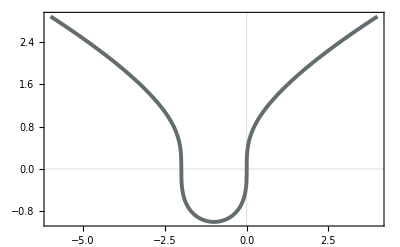

```mathematica
Remove[x,y];
y[x_]=CubeRoot[x(x+2)];
p1=Plot[y[x],{x,-6,4},PlotTheme->"Scientific",PlotStyle->{Thickness[0.007]},ColorFunction->"DarkRainbow"]
```

```mathematica
points=Table[{x,N[y[x]]},{x,-6,4}];
points//TableForm
```

-6 | 2.8845
-5 | 2.46621
-4 | 2.
-3 | 1.44225
-2 | 0.
-1 | -1.
0 | 0.
1 | 1.44225
2 | 2.
3 | 2.46621
4 | 2.8845

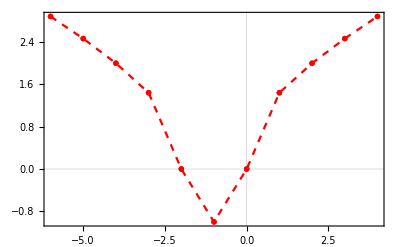

```mathematica
p2=ListPlot[points,Joined->True,Mesh->Full,PlotStyle->{PointSize[0.01],Red,Dashed},PlotTheme->"Scientific"]
```

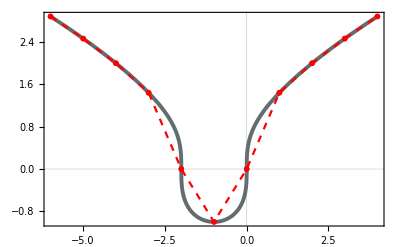

```mathematica
Show[p1,p2]
```

### 6.2. Building polynomial plot

Task. Plot polynomial .

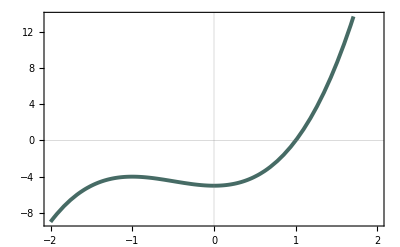

```mathematica
Remove[x,y];
y[x_]=-5+3 x^2+2 x^3;
Plot[y[x],{x,-2,2},PlotTheme->"Scientific",PlotStyle->{Thickness[0.007]},ColorFunction->"DarkRainbow"]
```

### 6.3. Build arbitrary explicitly defined function

Task. Plot

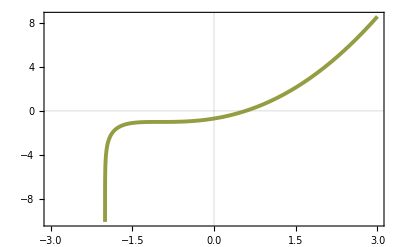

```mathematica
Clear[x,y];
y[x_]=2 x+x^2-(x+1)Log[x+2];
Plot[y[x],{x,-3,3},PlotTheme->"Scientific",PlotStyle->{Thickness[0.007]},ColorFunction->"DarkRainbow"]
```

### 6.4. Drawing Parametric Plots

Task. Build function . Build table of values on interval  and corresponding list plot.

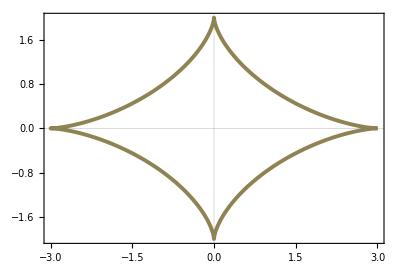

```mathematica
Remove[x,y,t];
x[t_]=3(Cos[t])^3;
y[t_]=2(Sin[t])^3;
p1=ParametricPlot[{x[t],y[t]},{t,0,2π},PlotTheme->"Scientific",PlotStyle->{Thickness[0.007],Blue},ColorFunction->"DarkRainbow"]
```

```mathematica
points=Table[{x[t],y[t]},{t,0,2π,π/8}];
npoints=N[points];
npoints//TableForm
```

3. | 0.
2.36574 | 0.112085
1.06066 | 0.707107
0.168128 | 1.57716
0. | 2.
-0.168128 | 1.57716
-1.06066 | 0.707107
-2.36574 | 0.112085
-3. | 0.
-2.36574 | -0.112085
-1.06066 | -0.707107
-0.168128 | -1.57716
0. | -2.
0.168128 | -1.57716
1.06066 | -0.707107
2.36574 | -0.112085
3. | 0.

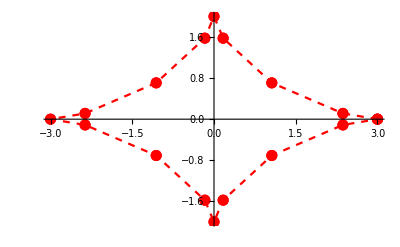

```mathematica
p2=ListPlot[npoints,Joined->True,Mesh->Full,PlotStyle->{PointSize[0.02],Red,Dashed}]
```

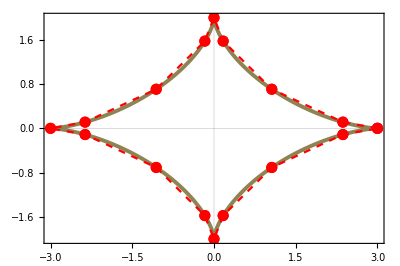

```mathematica
Show[p1,p2]
```

### 6.5. Drawing parametric plots

Task. Build plot  for interval .

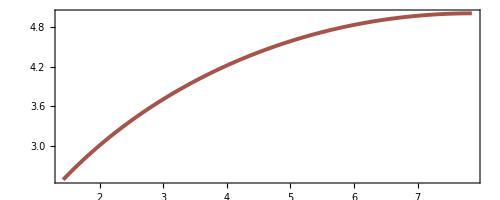

```mathematica
Clear[x,y,t]
x[t_]=5/2(t-Sin[t]);
y[t_]=5/2(1-Cos[t]);
p1=ParametricPlot[{x[t],y[t]},{t,π/2,π},PlotTheme->"Scientific",PlotStyle->{Thickness[0.007]},ColorFunction->"DarkRainbow"]
```

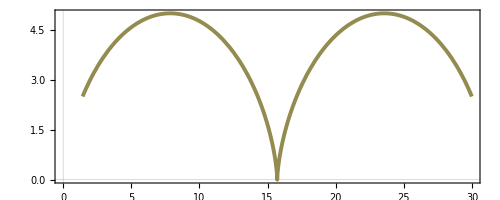

```mathematica
p2=ParametricPlot[{x[t],y[t]},{t,π/2,(7π)/2},PlotTheme->"Scientific",PlotStyle->{Thickness[0.007]},ColorFunction->"DarkRainbow"]
```

### 6.6. Build unexplicitly defined functions

Task. Build curve

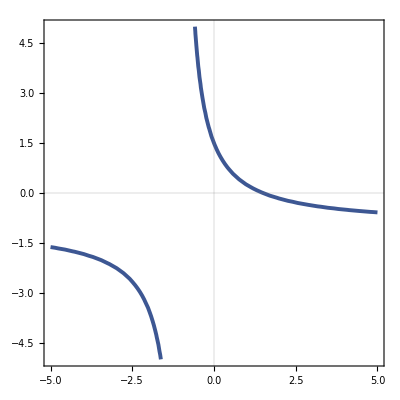

```mathematica
Remove[x,y,F];
F[x_,y_]=2x y+2x+2y-3;
ContourPlot[F[x,y]==0,{x,-5,5},{y,-5,5},PlotTheme->"Scientific",ColorFunction->"DarkRainbow",ContourStyle->{Thickness[0.007]}]
```